```mathematica
(* Modeling evaporative flux at unsaturated condition *)
```

```mathematica
(*Experiment data for unsaturated {water table (mm), flux (mm/day), SD flux (mm/day)}*)
(*H = 00 mm *)CS00={{15, 22.8, 1.692368723},{50 ,22.6 ,2.56},{60 ,22.3 ,1.655665703},{100 ,18.7 ,0.935776814},{140, 15.83550764 ,0.032173191},{185, 1.7,0.1}};
(*H = 05 mm *)CS05={{15 ,8.432803188 ,0.952999281},{50,8.294272084, 1.373242726},{100 ,7.924590886 ,0.93612619},{140, 9.132759353 ,1.23586792},{185 ,3.72 ,2.09}};
(*H = 10 mm *)CS10={{15, 6.814120392, 1.123055292},{50, 6.486910315, 1.14901281},{100, 5.574764303 ,0.915018004},{140 ,5.84271247 ,1.526689857},{185 ,2.03 ,1.29}};
```

```mathematica
(* Obtaining Equation 10 *)

ClearAll[H,F1,λ1,F2,λ2,data,xy,weights,fit];
(* Evaporative flux (mm/day) vs SHS mulch thickness (mm) *)
data={{0,22.8,1.69},{5,8.43,0.953},{10,6.81,1.123},{15,3.438,0.149399},{17.5,3.11333,1.59193},{20,2.66,0.59397}};

xy=data[[All,{1,2}]];
weights=(1/#^2&/@data[[All,3]]);
λ2=8.33692;

fit=NonlinearModelFit[xy,{F1 Exp[-λ1 H]+F2 Exp[-λ2 H],F1>0&&λ1>0&&F2>0},{{F1,13.},{λ1,0.09},{F2,10.}},H,Weights->weights];

(*Fitted coefficients and equation*)
fit["BestFitParameters"]
Normal[fit]

(*Weighted sum of squared residuals*)
Total[weights (fit["FitResiduals"]^2)]
```

{F1→13.4653,λ1→0.0900904,F2→9.33469}

9.33469 ⅇ^(-8.33692 H)+13.4653 ⅇ^(-0.0900904 H)

2.14069

```mathematica
Jw[H_]:=9.334692438764863 ⅇ^(-8.33692 H)+13.465307643049618 ⅇ^(-0.09009042515295114 H);(*H, SHS mulch thickness *)
Jd[H_,wt_]:=9.334692438764863 ⅇ^(-8.33692 (wt+H))+13.465307643049618 ⅇ^(-0.09009042515295114 (wt+H)); (*wt, water table (in mm)*)
```

```mathematica
ClearAll[a,b]
(*1. Define the dataset:{x,y}*)
data=Table[{CS00[[i,1]],CS00[[i,2]]},{i,1,Length[CS00]}];

(*2. Define the model function*)
model[x_,a_,b_]:=(1/2×(1-Tanh[(x-a)/b]))Jw[0]+(1-1/2×(1-Tanh[(x-a)/b]))Jd[0,x];

(*---NonlinearModelFit---*)
nlm=NonlinearModelFit[data,{model[x,a,b],a>0,b>0},{{a,150},{b,30}},x];

(*Display summary table containing Best-Fit Values,Standard Errors,t-Statistics,and p-Values*)
Print["=== NonlinearModelFit Parameter Summary ==="];
Quiet[nlm["ParameterTable"]]

(*Extract specific properties*)
Print["Best Fit Parameters: ",Quiet[nlm["BestFitParameters"]]];
Print["Standard Errors:     ",Quiet[nlm["ParameterErrors"]]];
Print["Residual SS (RSS):   ",Quiet[nlm["EstimatedVariance"]]*(Length[data]-2)];
```

=== NonlinearModelFit Parameter Summary ===

| Estimate | Standard Error | t-Statistic | P-Value
a | 150.321 | 5.10564 | 29.4421 | 7.92393×10^-6
b | 36.4033 | 9.01995 | 4.03587 | 0.0156573

Best Fit Parameters: {a→150.321,b→36.4033}

Standard Errors:     {5.10564,9.01995}

Residual SS (RSS):   10.912

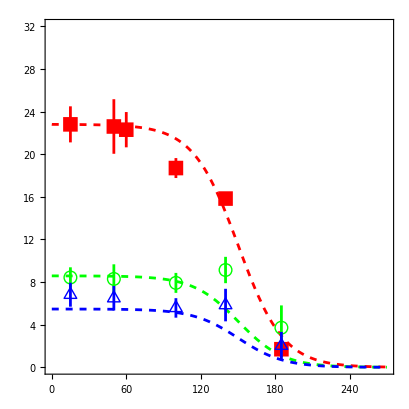

```mathematica
(* Obtaining Fig 7a *)
a=150.321;
b=36.403;
Show[{
Plot[{
(1/2×(1-Tanh[(wt-a)/b]))Jw[0]+(1-1/2×(1-Tanh[(wt-a)/b]))Jd[0,wt],
(1/2×(1-Tanh[(wt-a)/b]))Jw[5]+(1-1/2×(1-Tanh[(wt-a)/b]))Jd[5,wt],
(1/2×(1-Tanh[(wt-a)/b]))Jw[10]+(1-1/2×(1-Tanh[(wt-a)/b]))Jd[10,wt]
},{wt,0, 270},PlotRange->{{0,270},{0.,32}},PlotStyle->{{Dashed,Red},{Dashed,Green},{Dashed,Blue}}],
ListPlot[Table[{CS00[[i,1]],CS00[[i,2]]},{i,1,Length[CS00]}],Joined->False,PlotStyle->Red,PlotMarkers->{"■",15},PlotRange->{{0,270},{0,25}}],
ListPlot[Table[{{CS00[[i,1]],CS00[[i,2]]-CS00[[i,3]]},{CS00[[i,1]],CS00[[i,2]]+CS00[[i,3]]}},{i,1,Length[CS00]}],Joined->True,PlotStyle->Red],
ListPlot[Table[{CS05[[i,1]],CS05[[i,2]]},{i,1,Length[CS05]}],Joined->False,PlotStyle->Green,PlotMarkers->{"○",13},PlotRange->{{0,270},{0,25}}],
ListPlot[Table[{{CS05[[i,1]],CS05[[i,2]]-CS05[[i,3]]},{CS05[[i,1]],CS05[[i,2]]+CS05[[i,3]]}},{i,1,Length[CS05]}],Joined->True,PlotStyle->Green],
ListPlot[Table[{CS10[[i,1]],CS10[[i,2]]},{i,1,Length[CS10]}],Joined->False,PlotStyle->Blue,PlotMarkers->{"△",15},PlotRange->{{0,270},{0,25}}],
ListPlot[Table[{{CS10[[i,1]],CS10[[i,2]]-CS10[[i,3]]},{CS10[[i,1]],CS10[[i,2]]+CS10[[i,3]]}},{i,1,Length[CS10]}],Joined->True,PlotStyle->Blue]
},Frame->True,AspectRatio->1,ImageSize->{205,200}*2,FrameStyle->Directive[{15,Black,Thickness[0.00275]}]]
```

```mathematica
(*Sensitivity analysis*)
(*Given values and uncertainties*)
bMean=b;
bErr=9.02;
lcMean=81.0;
lcErr=1.0; 

(*Calculate nominal lp *)
lpNominal=2*Pi*bMean-lcMean;

(*Propagated standard error for lp*)
lpErr=Sqrt[(2*Pi*bErr)^2+(-1*lcErr)^2];

Print["Nominal lp (mm): ",lpNominal];
Print["Propagated Error sigma_lp (mm): ",lpErr];
Print["Range for lp: ",lpNominal-lpErr," to ",lpNominal+lpErr," mm"];
```

Nominal lp (mm): 147.727

Propagated Error sigma_lp (mm): 56.6832

Range for lp: 91.0436 to 204.41 mm

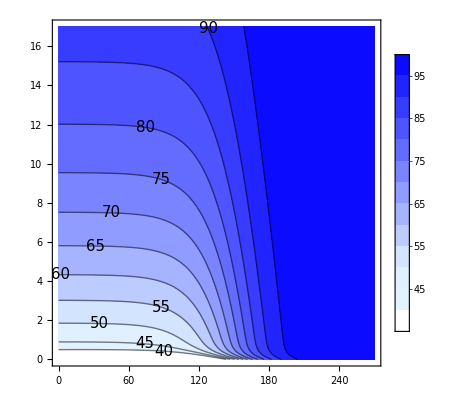

```mathematica
(* Obtaining Fig 7b *)
(* Equation 12 *)
func[wt_,H_]:=(1/2×(1-Tanh[(wt-a)/b]))Jw[H]+(1-1/2×(1-Tanh[(wt-a)/b]))Jd[H,wt];
ContourPlot[(func[0,0]-func[wt,H])/func[0,0] 100,{wt,0,270},{H,0,17},MaxRecursion->4,PerformanceGoal->"Quality",Contours->Range[40,100,5],ColorFunction->(Blend[{White,LightBlue,Blue},#]&),Frame->True,AspectRatio->1,ImageSize->{200,200}*2,FrameStyle->Directive[{15,Black,Thickness[0.00275]}],ContourLabels->(If[Abs[#2-(17/200) #1]<8,Text[Style[#3,15,Black,Background->None],{#1,#2}]]&),PlotLegends->BarLegend[Automatic,LegendLabel->Style[" ",15,Black],LabelStyle->{15,Black},LegendMarkerSize->375]]
```